```mathematica
Clear[f];
Vfene[r_, ϵ_, r0_, Δ_] := - (ϵ/2) Log[1 - ((r -r0)/Δ)^2];
Vmorse[x_, ϵ_, x0_, a_] := ϵ (1-Exp[ - a ( x - x0)])^2;
Vharm[r_, k_, r0_] := (k / 2) (r - r0)^2;
Vlj[r_, ϵ_, σ_] := 4 ϵ ( (σ/r)^12 - (σ/r)^6);
Vmod[θ_,a_,θ0_] := 1 - a(θ-θ0)^2;
Vsmooth[x_, b_, xc_] := b ( x-xc)^2;
```

```mathematica
dVsdr[x_,b_,xc_] := Evaluate[D[Vsmooth[x,b,xc],x]];
```

```mathematica
k=46; rc=0.6;r0=0.4; rhigh=0.58; rlow=0.22;
```

```mathematica
Vrc = Vharm[rc,k, r0]
```

0.92

```mathematica
dVhdr[rr_, kk_, rr0_]:=Evaluate[D[Vharm[rr,kk,rr0],rr]]
```

```mathematica
myVar=FindRoot[ {
Evaluate[Vharm[rlow,k,r0]]- Vrc== k Vsmooth[rlow,b, xc],
dVhdr[rlow,k,r0] == k dVsdr[rlow,b,xc]
}, {{b,-10}, {xc, rlow-0.1}}, MaxIterations-> 10000];
blow=b/.myVar
xclow= xc/.myVar
```

-2.13158

0.177778

```mathematica
myVar=FindRoot[ {
Evaluate[Vharm[rhigh,k,r0]]- Vrc== k Vsmooth[rhigh,b, xc],
dVhdr[rhigh,k,r0] == k dVsdr[rhigh,b,xc]
},{{b,10},{xc,rhigh+0.1}}, MaxIterations-> 10000];
bhigh=b/.myVar
xchigh= xc/.myVar
```

-2.13158

0.622222

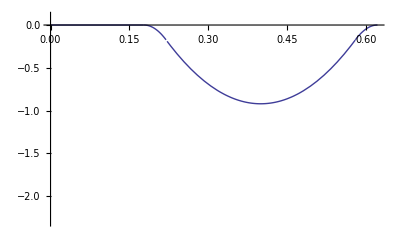

```mathematica
f2[r_] :=   Piecewise[{
{0 ,r <xclow },
{k Vsmooth[r,blow,xclow], xclow≤ r < rlow },
{Vharm[r,k,r0]-Vrc, rlow≤ r < rhigh},
{k Vsmooth[r, bhigh,xchigh], rhigh≤r<xchigh},
{0, r> xchigh} 
}]
Plot[f2[r], {r, 0, xchigh}, PlotRange->{{0,xchigh},{-2.3,0.1}}]
```